## Функции

## Простой синтаксис

Функция, которая возводит в квадрат и прибавляет единицу

```mathematica
mySqr[x_] := x^2 + 1
```

```mathematica
mySqr[{1, 2}]
```

{2,5}

```mathematica
{1, 2}^2 + 1
```

{2,5}

## Перегрузка

Функция, которая сохраняет строку в файл .txt, а матрицу в .dat

```mathematica
Head[table1]
```

List

```mathematica
Head[ВсеЧтоУгодно[1, 2, 3]]
```

ВсеЧтоУгодно

```mathematica
ВсеЧтоУгодно[1, 2, 3]
```

ВсеЧтоУгодно[1,2,3]

```mathematica
table1 = Table[{i, i^2}, {i, 1, 10}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

```mathematica
string1 = "my string 1"
```

my string 1

```mathematica
myExport[table_List] := Export["myFile.dat", table, "Table"]
```

```mathematica
myExport[table_String] := Export["myFile.txt", table, "String"]
```

```mathematica
?myExport
```

```mathematica
myExport[string1]
```

myFile.txt

```mathematica
myExport[table1]
```

myFile.dat

## Аргументы по умолчанию

Скользящее среднее и период усреднения по умолчанию

```mathematica
arr1 = Table[Sin[x] + RandomReal[0.1], {x, 0, 20, 0.025}];
```

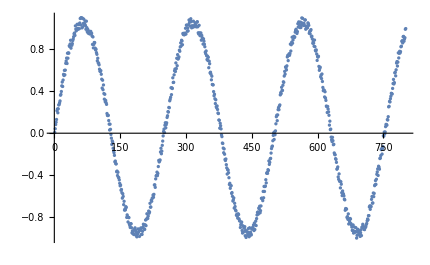

```mathematica
ListPlot[arr1]
```

```mathematica
ma[arr_List, period_Integer: 10] := Table[
{i + period, Mean[arr[[i ;; i + period]]]}, 
{i, 1, Length[arr] - period}
]
```

```mathematica
Manipulate[ListPlot[{arr1, ma[arr1, period]}, Joined->{False, True}], {period, 3, 50, 1}]
```

```mathematica
f[x_Real: 10.0, y_Integer: 10, z_String: "string"] := {x, y, z}
```

```mathematica
f[13, "my string"]
```

{10.,13,my string}

```mathematica
f1[x_: 10, y_: 10.0, z_: "string"] := {x, y, z}
```

```mathematica
f1["my string"]
```

{my string,10.,string}

## Скобочки и многострочный код

Импорт всех файлов из указанной папки в несколько действий

```mathematica
myImport[dir_String] := (
files = FileNames["*.txt", {dir}]; 
fileLen = Length[files]; 
Table[
file = files[[i]]; 
text = Import[file, "String"];
lines = Rest[StringSplit[text, "\n"]]; 
lineLen = Length[lines]; 
file -> Table[
line = StringTrim[lines[[j]]]; 
columns = StringSplit[line, " "]; 
columnLen = Length[columns];
Table[ToExpression[columns[[k]]], {k, 1, columnLen}],
{j, 1, lineLen}
], 
{i, 1, fileLen}
]
)
```

```mathematica
myImport["C:\\Users\\Kirill\\Desktop"]
```

{C:\Users\Kirill\Desktop\file1.txt→{{1,2.01},{2,2.93},{3,4.1},{5,6.8},{6,9.1},{7,11}},C:\Users\Kirill\Desktop\file2.txt→{{1,2},{2,3},{3,4},{5,7},{6,9},{7,11}}}

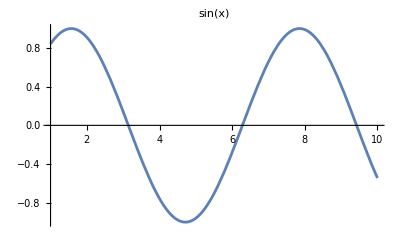

```mathematica
text = "sin(x)"; 
Plot[Sin[x], {x, 1, 10}, PlotLabel->text]
```

## Как использовать локальные переменные

Но чем плох прием показанный выше? Допустим у нас уже где-то используется переменная.

```mathematica
myImport[dir_String] := Module[{files, fileLen, file, text, lines, lineLen, columns, columnLen, line}, 

files = FileNames["*.txt", {dir}]; 
fileLen = Length[files]; 
Table[
file = files[[i]]; 
text = Import[file, "String"];
lines = Rest[StringSplit[text, "\n"]]; 
lineLen = Length[lines]; 
file -> Table[
line = StringTrim[lines[[j]]]; 
columns = StringSplit[line, " "]; 
columnLen = Length[columns];
Table[ToExpression[columns[[k]]], {k, 1, columnLen}],
{j, 1, lineLen}
], 
{i, 1, fileLen}
]
]
```

```mathematica
x = 1; y = 2; z = y  + y; z
```

4

```mathematica
x
```

1

```mathematica
y
```

2

```mathematica
z
```

4

## “Чистые” функции

Если эти назвают чистыми, то те что выше грязными??? о_О

```mathematica
x = 1
```

1

```mathematica
f[x_] := x + 1
```

```mathematica
myFunc = Function[{x, y, z}, 
x + y + z
]
```

Function[{x,y,z},x+y+z]

```mathematica
myFunc[1, 2, 3]
```

6

```mathematica
Function[{x, y, z}, x + y + z][1, 2, 3]
```

6

```mathematica
#1 + #2 + #3&[1, 2, 3]
```

6

```mathematica
Sqrt[x^3 + 2 * x^2 + 3 * x + 4]
```

√10

```mathematica
arr = RandomReal[10, 10]
```

{0.471235,8.43712,8.3258,5.25273,7.62291,7.38774,7.39446,6.23944,9.154,4.33018}

```mathematica
Table[Sqrt[#^3 + 2 * #^2 + 3 * # + 4]&[arr[[i]]], {i, 1, 10}]
```

{2.44182,27.7899,27.2901,14.828,24.2084,23.2064,23.2348,18.5333,31.0825,11.6484}

## Обработка строк

#### Все что угодно можно превратить в строку

```mathematica
ToString[{1, 2, 3}]
```

```mathematica
ExportString[{1, 2, 3}, "String"]
```

#### Как строку превратить в набор байт

```mathematica
StringToByteArray["0000"]
```

```mathematica
ToCharacterCode["0000"]
```

#### Кодировки

```mathematica
text = Import["C:\\Users\\Kirill\\Desktop\\text.txt"]
```

òåêñò íà ðóññêîì

```mathematica
chars = ToCharacterCode[text, "Unicode"]
```

{242,229,234,241,242,32,237,224,32,240,243,241,241,234,238,236}

```mathematica
FromCharacterCode[chars, "WindowsCyrillic"]
```

текст на русском

#### Как узнать длину строки

```mathematica
StringLength["1234567"]
```

#### Как получить подстроку

```mathematica
StringTake["StartTime = 12:00:00", -8]
```

12:00:00

```mathematica
StringExtract["предложение из нескольких слов", 3]
```

нескольких

```mathematica
StringExtract[
"первый заголовок
	второй заголовок:значение", 
	"\n\t" -> 2, ":" -> 2
]
```

значение

#### Как найти позицию подстроки в строке

```mathematica
StringPosition["123456789012345", "45"]
```

{{4,5},{14,15}}

#### Как обрезать края

```mathematica
StringTrim["
	1234 1234 

       "]
```

1234 1234

```mathematica
StringTrim["<1234 1234>", {"<", ">"}]
```

1234 1234

#### Как соединить строки

```mathematica
StringJoin["string ", "string2"]
StringJoin[{"string ", "string2"}]
StringJoin["strings: ", {"string ", "string2"}]
"strings: " <> "string " <> "string2"
```

string string2

string string2

strings: string string2

strings: string string2

#### Как сравнить две строки

#### Как вытащить из строки данные соответствующие шаблону

#### Подробнее про шаблоны

#### Специальные константы

#### Пример как разобрать LAS

```mathematica
data1=ImportString["x  delta
0  -12.65344814
100  -7.030795084
200  4.66877579
300  11.68820361
400  7.573501303
500  -3.892446622
600  -12.16786862
700  -9.644225765
800  1.358439281
900  10.72443831
1000  9.842671744","Table"]
```

```mathematica
{{"x","delta"},{0,-12.65344814},{100,-7.030795084},{200,4.66877579},{300,11.68820361},{400,7.573501303},{500,-3.892446622},{600,-12.16786862},{700,-9.644225765},{800,1.358439281},{900,10.72443831},{1000,9.842671744}}
```

```mathematica
data2=Rest[data1]
```

{{0,-12.6534},{100,-7.0308},{200,4.66878},{300,11.6882},{400,7.5735},{500,-3.89245},{600,-12.1679},{700,-9.64423},{800,1.35844},{900,10.7244},{1000,9.84267}}

```mathematica
weigth[x_, xi_, p_: 2] := EuclideanDistance[x, xi]^-p
```

```mathematica
delta[x_, p_:2] := 
If[MemberQ[data2[[All, 1]], x],Last @ SelectFirst[#[[1]] == x&] @ data2,  
Sum[point[[2]] * weigth[x, point[[1]], p], {point, data2}] / Sum[weigth[x, point[[1]], p], {point, data2}]
]
```

```mathematica
Manipulate[Show[Plot[delta[x, p], {x, 0, 1000}, PlotTheme->"Detailed", PlotLegends->{"delta(x)"}], 
ListPlot[data2, PlotStyle->Directive[Red, PointSize[Large]]]
], {p, 1, 4, 1}]
```